# Supplement to TASI Lecture three of “Quantum Information Science for Particle Theorists” Reproduces the area law for 3+1 dimensional discretized scalar field theory, first derived by Srednicki in arXiv:hep-th/9303048.

THIS NOTEBOOK CREATED BY J. LYKKEN

## Compute the entanglement entropy The radius of the complete discretized system of oscillators is R = (M+1/2)*a where “a” is the radial lattice spacing The radius of the inner sphere R_B = (n+1/2)*a We vary n over values from 1 to some nmax <= M We also sum over angular momenta “l” up to lmax=1000. This is enough to see the area law. It make take a few minutes to run.

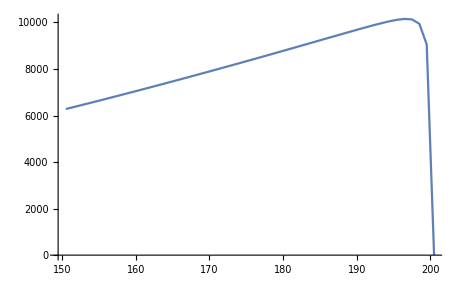

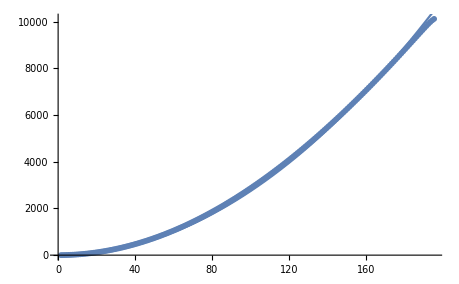

```mathematica
M=200; (* Infrared cutoff: the discrete radius takes values j=1,...M *)
nmax=200; (* Largest value for the radius R_B is R_B = nmax + 1/2 *)
lmax=1000; (* Ultraviolet cutoff for the angular momentum eigenvalue l *)
Clear[s];

(* First we need to construct the coupling matrix K_{ij} of the oscillators: *)
(* K is an MxM matrix, initialize it with zeroes: *)
Do[ (* for all l values up to lmax *)
(* K is an MxM matrix, initialize it with zeroes: *)
K=Table[0,{i,1,M},{j,1,M}];
(* Put in the diagonal entries: *)
Do[ K[[j,j]]=N[(j+1/2)^2/j^2+(j−1/2)^2/j^2+l (l+1)/j^2],{j,2,M}];
(* j=1 is a special case: *)
K[[1,1]]=N[l(l+1)+(3/2)^2];
(* Put in the off-diagonal entries: *)
Do[K[[j,j+1]]=N[−(j+1/2)^2/j/(j+1)];
K[[j+1,j]]=K[[j,j+1]],{j,1,M−1}];

(* Find the basis that diagonalizes K : *)
u=Eigensystem[K];
u1=u[[1]];
u2=u[[2]];
(* Construct the 2-pnt correlator X out of this: *)
X=Transpose[u2].DiagonalMatrix[1/Sqrt[u1]/2].u2;
(* Construct the 2-pnt correlator P: *)
P=Transpose[u2].DiagonalMatrix[Sqrt[u1]/2].u2;

Do[(* for all n values up to nmax *)
(* The next step is the equivalent of taking the partial trace of
the density matrix over the oscillators inside the R_B sphere: *)
XV=Take[X,{1,n},{1,n}]; (* Truncate to the n x n submatrix: *)
PV=Take[P,{1,n},{1,n}]; (* Truncate to the n x n submatrix: *)
c=Sqrt[Eigenvalues[XV.PV]];
(* Here is the entropy: *)
s[l,n]=(c+1/2).Log[c+1/2]−(c−1/2+10^(−10)).Log[c−1/2+10^(−10)],{n,1,nmax}],
{l,0,lmax}]

entropy=Table[{n+1/2,Sum[(2 l+1) s[l,n],{l,0,lmax}]},{n,1,nmax-5}];
entropy2=Table[{n+1/2,Sum[(2 l+1) s[l,n],{l,0,lmax}]},{n,nmax-50,nmax}];

aa=ListPlot[entropy];
aa2=ListLinePlot[entropy2];
Show[aa2]
(* Try to fit to a quadratic:*)
Clear[x];
fun=Fit[entropy,{x^2},x];
bb=Plot[fun,{x,1,nmax-5}];
Show[aa,bb]
```

## Notes end here for now